# Title

Author Name

Abstract

## Section

XXXX:

```mathematica
unbalanceSetFunction//ClearAll
QuadraticFunction//ClearAll
MostUnbalancedSets//ClearAll
RandomEdgeMixer//ClearAll
unbalanceSetFunction[graph_?GraphQ,set_]:=Length[Cases[IncidenceList[graph,Alternatives@@set],Alternatives@@set->Except[Alternatives@@set]]]-Length[Cases[IncidenceList[graph,Alternatives@@set],Except[Alternatives@@set]->Alternatives@@set]]-Length[Cases[IncidenceList[graph,Alternatives@@set],Except[Alternatives@@set]<->Alternatives@@set|Alternatives@@set<->Except[Alternatives@@set]]]
QuadraticFunction[graph_?GraphQ]:=(unbalanceSetFunction[graph,#1]&)/@Sort[VertexList[graph]].Array[Indexed[x,##1]&,VertexCount[graph]]+Total[(2 Times@@(Indexed[x,#1]&)/@{First[#1],Last[#1]}&)/@EdgeList[graph,_<->_]]
MostUnbalancedSets[graph_?GraphQ]:=Quiet@Block[{max,vertexCount},vertexCount=VertexCount[graph];max=First[Maximize[QuadraticFunction[graph],(0≤#1≤1&)/@Array[Indexed[x,##1]&,vertexCount],(#1∈Integers&)/@Array[Indexed[x,##1]&,vertexCount]]];(DeleteCases[Range[vertexCount] Values[Association[#1]],0]&)/@Solve[QuadraticFunction[graph]==max&&And@@(0≤#1≤1&)/@Array[Indexed[x,##1]&,vertexCount],(#1∈Integers&)/@Array[Indexed[x,##1]&,vertexCount]]];
MostUnbalancedSetsEquation[graph_?GraphQ]:=Quiet@Block[{maxB,vertexCountB},vertexCountB=VertexCount[graph];maxB=First[Maximize[QuadraticFunction[graph],(0≤#1≤1&)/@Array[Indexed[x,##1]&,vertexCountB],(#1∈Integers&)/@Array[Indexed[x,##1]&,vertexCountB]]];(DeleteCases[Range[vertexCountB]* Values[Association[#1]],0]&)/@HoldForm@Solve[QuadraticFunction[graph]==maxB&&And@@(0≤#1≤1&)/@Array[Indexed[x,##1]&,vertexCountB],(#1∈Integers&)/@Array[Indexed[x,##1]&,vertexCountB]]];
MixedEulerianGraphQ[graph_?GraphQ]:=Quiet@(MemberQ[MostUnbalancedSets[graph],{}])
RandomEdgeMixer[graph_]:=Block[{edges},edges=EdgeList[graph];Graph@Table[RandomChoice[{1/2,1/4,1/4}->{First[k]<->Last[k],Last[k]->First[k],First[k]->Last[k]}],{k,edges}]]
RandomEdgeMixer[graph_,edgeweights_?ListQ]:=Block[{edges},edges=EdgeList[graph];Graph@Table[RandomChoice[edgeweights->{First[k]<->Last[k],First[k]->Last[k],Last[k]->First[k],}],{k,edges}]]/;Total[edgeweights]==1&&Length[edgeweights]==1&&AllTrue[edgeweights,0<=#<=1&]
```

#### random edge mixer tests

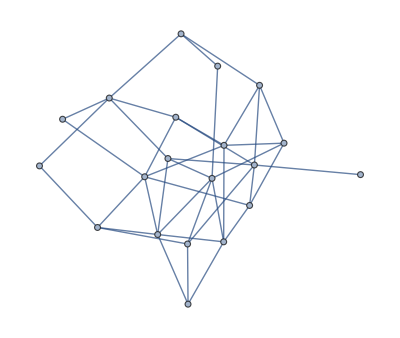

```mathematica
RandomGraph[{20,40}]
```

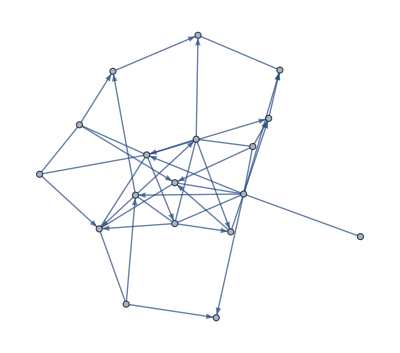

```mathematica
RandomEdgeMixer[RandomGraph[{20,40}]]
```

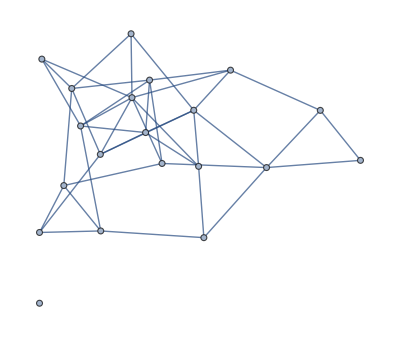
RandomEdgeMixer[-Graphics-,{1/2,1/3,1/3}]

```mathematica
RandomEdgeMixer[RandomGraph[{20,40}],{1/2,1/3,1/3}]
```

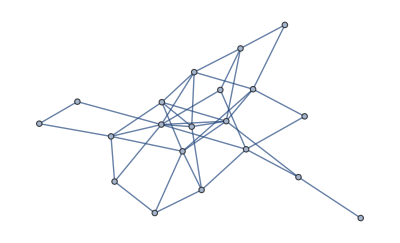
RandomEdgeMixer[-Graphics-,{1/2,1/4,1/8,1/8}]

```mathematica
RandomEdgeMixer[RandomGraph[{20,40}],{1/2,1/4,1/8,1/8}]
```

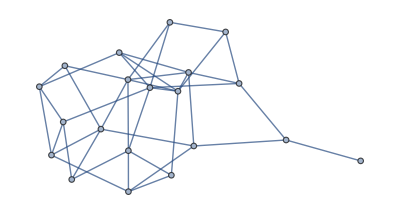
RandomEdgeMixer[-Graphics-,{1,1,-1}]

```mathematica
RandomEdgeMixer[RandomGraph[{20,40}],{1,1,-1}]
```

#### work

```mathematica
First[Select[ConnectedGraphQ[GraphData[#]]&][Take[GraphData["Eulerian"],50]]]
```

{6,135}

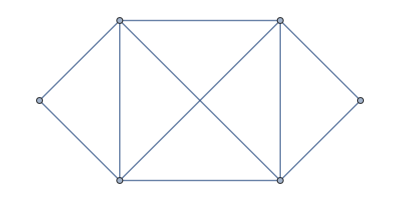

```mathematica
GraphData[First[Select[ConnectedGraphQ[GraphData[#]]&][Take[GraphData["Eulerian"],50]]]]
```

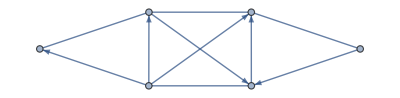

```mathematica
RandomEdgeMixer[GraphData[First[Select[ConnectedGraphQ[GraphData[#]]&][Take[GraphData["Eulerian"],50]]]]]
```

```mathematica
QuadraticFunction[RandomEdgeMixer[GraphData[First[Select[ConnectedGraphQ[GraphData[#]]&][Take[GraphData["Eulerian"],50]]]]]]
```

-2 x1-2 x2-4 x3+2 x1 x3-2 x4+2 x3 x4-2 x5+2 x2 x5+2 x3 x5-2 x6+2 x1 x6+2 x2 x6+2 x3 x6

RandomGeneratorState[…]

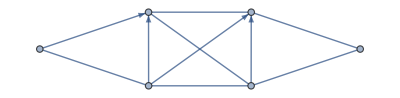

{{1,4},{1,4,6},{1,2,4,6}}

RandomGeneratorState[…]

```mathematica
SeedRandom[1];
$RandomGeneratorState
RandomEdgeMixer[GraphData[First[Select[ConnectedGraphQ[GraphData[#]]&][Take[GraphData["Eulerian"],50]]]]]//BlockRandom
MostUnbalancedSets[RandomEdgeMixer[GraphData[First[Select[ConnectedGraphQ[GraphData[#]]&][Take[GraphData["Eulerian"],50]]]]]]//BlockRandom
$RandomGeneratorState
```

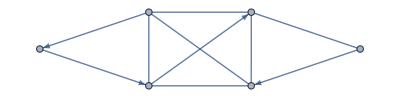
(DeleteCases[Range[vertexCountB] Values[Association[#1]],0]&)[Solve[QuadraticFunction[-Graphics-]==maxB&&And@@(0≤#1≤1&)/@Array[Indexed[x,##1]&,vertexCountB],(#1∈ℤ&)/@Array[Indexed[x,##1]&,vertexCountB]]]

```mathematica
MostUnbalancedSetsEquation[RandomEdgeMixer[GraphData[First[Select[ConnectedGraphQ[GraphData[#]]&][Take[GraphData["Eulerian"],50]]]]]]
```

```mathematica
QuadraticFunction[GraphData[First[Select[ConnectedGraphQ[GraphData[#]]&][Take[GraphData["Eulerian"],50]]]]]
```

-4 x1-2 x2-4 x3+2 x1 x3-2 x4+2 x1 x4+2 x3 x4-4 x5+2 x1 x5+2 x2 x5+2 x3 x5-4 x6+2 x1 x6+2 x2 x6+2 x3 x6+2 x5 x6

```mathematica
Maximize[QuadraticFunction[GraphData[First[Select[ConnectedGraphQ[GraphData[#]]&][Take[GraphData["Eulerian"],50]]]]],(0≤#1≤1&)/@Array[Indexed[x,##1]&,6],(#1∈Integers&)/@Array[Indexed[x,##1]&,6]]
```

{0,{x1→0,x2→0,x3→0,x4→0,x5→0,x6→0}}

```mathematica
Solve[QuadraticFunction[GraphData[First[Select[ConnectedGraphQ[GraphData[#]]&][Take[GraphData["Eulerian"],50]]]]]==0&&And@@(0≤#1≤1&)/@Array[Indexed[x,##1]&,6],(#1∈Integers&)/@Array[Indexed[x,##1]&,6]]
```

{{x1→0,x2→0,x3→0,x4→0,x5→0,x6→0},{x1→1,x2→1,x3→1,x4→1,x5→1,x6→1}}

```mathematica
Maximize[QuadraticFunction[-Graphics-],(0≤#1≤1&)/@Array[Indexed[x,##1]&,6],(#1∈Integers&)/@Array[Indexed[x,##1]&,6]]
```

{2,{x1→1,x2→0,x3→0,x4→1,x5→0,x6→0}}

```mathematica
Solve[QuadraticFunction[-Graphics-]==2&&And@@(0≤#1≤1&)/@Array[Indexed[x,##1]&,6],(#1∈Integers&)/@Array[Indexed[x,##1]&,6]]
```

{{x1→1,x2→0,x3→0,x4→1,x5→0,x6→0},{x1→1,x2→0,x3→0,x4→1,x5→0,x6→1},{x1→1,x2→1,x3→0,x4→1,x5→0,x6→1}}

```mathematica
MostUnbalancedSets[-Graphics-]
```

{{1,4},{1,4,6},{1,2,4,6}}

```mathematica
PossibleEulerianGraphQ//ClearAll
PossibleEulerianGraphQ[graph_?ConnectedGraphQ]:=Block[{maxdata,order},order=VertexCount[graph];maxdata=Maximize[QuadraticFunction[graph],(0≤#1≤1&)/@Array[Indexed[x,##1]&,order],(#1∈Integers&)/@Array[Indexed[x,##1]&,order]]]
```

```mathematica
PossibleEulerianGraphQ[-Graphics-]
```

{2,{x1→1,x2→0,x3→0,x4→1,x5→0,x6→0}}

```mathematica
Select[ConnectedGraphQ[GraphData[#]]&][Select[VertexCount[GraphData[#]]<140&][Take[GraphData["Eulerian"],100]]]
```

{{6,135},{6,150},{7,112},{7,173},{7,204},{7,308},{7,461},{7,583},{7,631},{7,689},{7,711},{7,750},{7,836},{7,859},{7,884},{7,885},{7,926},{7,936},{7,957},{7,970},{7,985},{7,1010},{7,1015},{7,1020},{8,579},{8,7674},{8,8186},{8,8699},{8,8726},{8,10585},{8,10935},{8,10982},{8,11242},{8,11853},{8,12214},{8,12333},{8,12339},{AGIncidenceMinusParallelClass,{2,4}},{AGIncidenceMinusParallelClass,{2,8}},{Andrasfai,4},{Andrasfai,6},{Andrasfai,8},{Andrasfai,10},{Antiprism,4},{Antiprism,5},{Antiprism,6},{Antiprism,7},{Antiprism,8},{Antiprism,9},{Antiprism,10},{Antiprism,11},{Antiprism,12},{Antiprism,13},{Antiprism,14},{Antiprism,15},{Antiprism,16},{Antiprism,17},{Antiprism,18},{Antiprism,19},{Antiprism,20},{Antiprism,21},{Antiprism,22},{Antiprism,23},{Antiprism,24},{Antiprism,25},{ArcTransitive,{21,7}},{ArcTransitive,{21,8}},{ArcTransitive,{24,9}},{ArcTransitive,{24,10}},{ArcTransitive,{24,12}},{ArcTransitive,{24,14}},{ArcTransitive,{24,15}},{ArcTransitive,{24,17}},{ArcTransitive,{24,18}},{ArcTransitive,{24,27}},{ArcTransitive,{25,3}},{ArcTransitive,{25,4}},{ArcTransitive,{27,2}},{ArcTransitive,{27,5}},{ArcTransitive,{27,7}},{ArcTransitive,{27,9}},{ArcTransitive,{27,10}},{ArcTransitive,{27,11}},{ArcTransitive,{27,12}},{ArcTransitive,{27,17}},{ArcTransitive,{28,4}},{ArcTransitive,{28,6}}}

```mathematica
(Select[ConnectedGraphQ[GraphData[#]]&]@*Select[VertexCount[GraphData[#]]<140&])[Take[GraphData["Eulerian"],100]]
```

{{6,135},{6,150},{7,112},{7,173},{7,204},{7,308},{7,461},{7,583},{7,631},{7,689},{7,711},{7,750},{7,836},{7,859},{7,884},{7,885},{7,926},{7,936},{7,957},{7,970},{7,985},{7,1010},{7,1015},{7,1020},{8,579},{8,7674},{8,8186},{8,8699},{8,8726},{8,10585},{8,10935},{8,10982},{8,11242},{8,11853},{8,12214},{8,12333},{8,12339},{AGIncidenceMinusParallelClass,{2,4}},{AGIncidenceMinusParallelClass,{2,8}},{Andrasfai,4},{Andrasfai,6},{Andrasfai,8},{Andrasfai,10},{Antiprism,4},{Antiprism,5},{Antiprism,6},{Antiprism,7},{Antiprism,8},{Antiprism,9},{Antiprism,10},{Antiprism,11},{Antiprism,12},{Antiprism,13},{Antiprism,14},{Antiprism,15},{Antiprism,16},{Antiprism,17},{Antiprism,18},{Antiprism,19},{Antiprism,20},{Antiprism,21},{Antiprism,22},{Antiprism,23},{Antiprism,24},{Antiprism,25},{ArcTransitive,{21,7}},{ArcTransitive,{21,8}},{ArcTransitive,{24,9}},{ArcTransitive,{24,10}},{ArcTransitive,{24,12}},{ArcTransitive,{24,14}},{ArcTransitive,{24,15}},{ArcTransitive,{24,17}},{ArcTransitive,{24,18}},{ArcTransitive,{24,27}},{ArcTransitive,{25,3}},{ArcTransitive,{25,4}},{ArcTransitive,{27,2}},{ArcTransitive,{27,5}},{ArcTransitive,{27,7}},{ArcTransitive,{27,9}},{ArcTransitive,{27,10}},{ArcTransitive,{27,11}},{ArcTransitive,{27,12}},{ArcTransitive,{27,17}},{ArcTransitive,{28,4}},{ArcTransitive,{28,6}}}

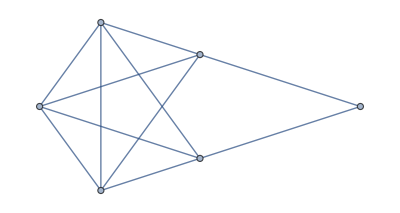
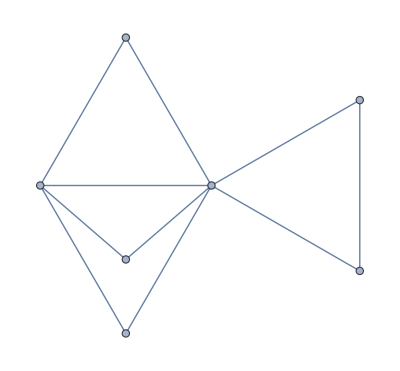
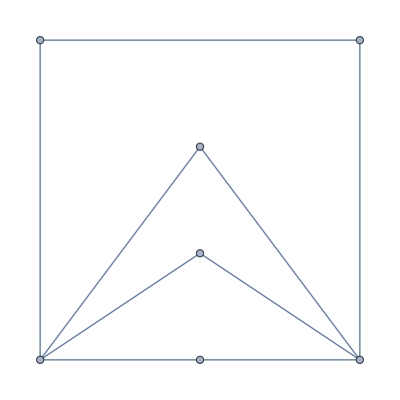
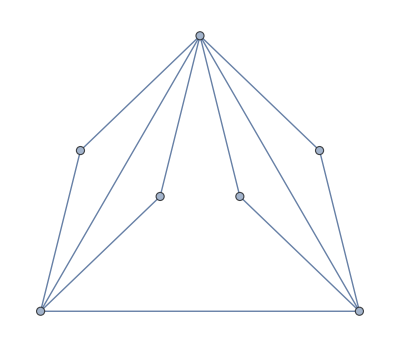
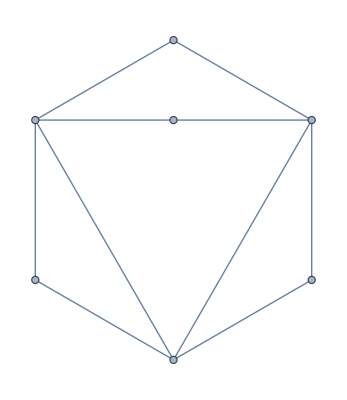
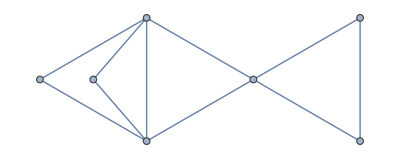
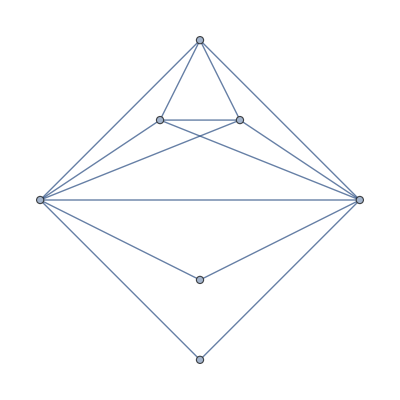
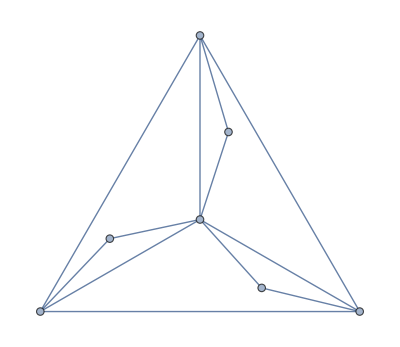
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graph[GraphData[#],ImageSize->Tiny]&/@((Select[ConnectedGraphQ[GraphData[#]]&]@*Select[VertexCount[GraphData[#]]<140&]@*Select[EdgeCount[GraphData[#]]<403&])[Take[GraphData["Eulerian"],100]])
```

```mathematica
MonitorProgress[First[PossibleEulerianGraphQ[#]]&/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
NPossibleEulerianGraphQ//ClearAll
NPossibleEulerianGraphQ[graph_?ConnectedGraphQ]:=Block[{maxdata,order},order=VertexCount[graph];maxdata=NMaximize[QuadraticFunction[graph],(0≤#1≤1&)/@Array[Indexed[x,##1]&,order],(#1∈Integers&)/@Array[Indexed[x,##1]&,order]]]
```

```mathematica
MonitorProgress[First[NPossibleEulerianGraphQ[#]]&/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
ZeroCheckPossibleEulerianGraphQ//ClearAll
ZeroCheckPossibleEulerianGraphQ[graph_?ConnectedGraphQ]:=Block[{maxdata,order},order=VertexCount[graph];maxdata=Maximize[QuadraticFunction[graph],(0≤#1≤1&)/@Array[Indexed[x,##1]&,order],(#1∈Integers&)/@Array[Indexed[x,##1]&,order]];First[maxdata]==0]
```

```mathematica
MonitorProgress[ZeroCheckPossibleEulerianGraphQ[#]&/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
TimeConstrained[ZeroCheckPossibleEulerianGraphQ[-Graphics-],10]
```

$Aborted

```mathematica
SeedRandom[1];
$RandomGeneratorState
RandomEdgeMixer[RandomGraph[{100,140}]]//BlockRandom
First@TakeLargestBy[ConnectedGraphComponents[RandomEdgeMixer[RandomGraph[{100,140}]]],VertexCount,1]//BlockRandom
TimeConstrained[ZeroCheckPossibleEulerianGraphQ@First@TakeLargestBy[ConnectedGraphComponents[RandomEdgeMixer[RandomGraph[{100,140}]]],VertexCount,1],10]//BlockRandom
$RandomGeneratorState
```

RandomGeneratorState[…]

-Graphics-

-Graphics-

-3 x1-4 x3-2 x4-x5+x6-3 x8-2 x9-x10-x11-x12-4 x13-2 x14-3 x15-2 x16+2 x18 x19-3 x20-2 x21+2 x16 x21-3 x22-3 x23-2 x24-x25+2 x10 x25-4 x26-2 x27+2 x8 x27-4 x28+x29-x30-3 x31-2 x32-5 x33+x34+2 x12 x34-2 x35+2 x29 x35-2 x36+2 x5 x36-4 x37+x38-2 x39-3 x40+2 x7 x40+2 x29 x40-3 x41+x42-x44-2 x45+x46-3 x47+2 x22 x47-2 x48-x49+2 x28 x49-3 x50+2 x34 x50-x51-2 x52+2 x34 x52-2 x53-x54+2 x19 x54+2 x23 x54-4 x55-x56-2 x57-3 x58-x59+2 x6 x60-5 x61+2 x47 x61-4 x64+2 x58 x64-3 x65-4 x66+2 x63 x66-2 x68+2 x27 x68+x69+2 x36 x69+2 x50 x69+2 x61 x70-2 x71+2 x53 x71-5 x72+2 x69 x72-2 x73+2 x29 x73-x74+2 x32 x74+2 x52 x74-x75-3 x76+2 x17 x76+2 x21 x76+2 x50 x76+2 x64 x76-6 x77+2 x49 x77+2 x24 x78+2 x60 x78+2 x36 x79+2 x40 x79+2 x27 x82+2 x75 x82+2 x51 x85+2 x74 x85+2 x83 x85+2 x85 x86+2 x11 x87+2 x16 x87+2 x76 x87+2 x5 x88+2 x40 x89+2 x68 x89+2 x60 x90+2 x32 x94+2 x38 x94+2 x6 x95+2 x19 x95+2 x29 x95+2 x54 x95+2 x74 x95+2 x22 x96+2 x80 x96+2 x82 x96+2 x90 x97+2 x1 x98+2 x11 x99+2 x45 x99+2 x65 x99+2 x1 x100+2 x23 x100+2 x47 x100+2 x58 x100+2 x71 x100==0

RandomGeneratorState[…]

```mathematica
PossibleEulerianGraphQ[-Graphics-]
```

Maximize[-3 x1-4 x3-2 x4-x5+x6-3 x8-2 x9-x10-x11-x12-4 x13-2 x14-3 x15-2 x16+2 x18 x19-3 x20-2 x21+2 x16 x21-3 x22-3 x23-2 x24-x25+2 x10 x25-4 x26-2 x27+2 x8 x27-4 x28+x29-x30-3 x31-2 x32-5 x33+x34+2 x12 x34-2 x35+2 x29 x35-2 x36+2 x5 x36-4 x37+x38-2 x39-3 x40+2 x7 x40+2 x29 x40-3 x41+x42-x44-2 x45+x46-3 x47+2 x22 x47-2 x48-x49+2 x28 x49-3 x50+2 x34 x50-x51-2 x52+2 x34 x52-2 x53-x54+2 x19 x54+2 x23 x54-4 x55-x56-2 x57-3 x58-x59+2 x6 x60-5 x61+2 x47 x61-4 x64+2 x58 x64-3 x65-4 x66+2 x63 x66-2 x68+2 x27 x68+x69+2 x36 x69+2 x50 x69+2 x61 x70-2 x71+2 x53 x71-5 x72+2 x69 x72-2 x73+2 x29 x73-x74+2 x32 x74+2 x52 x74-x75-3 x76+2 x17 x76+2 x21 x76+2 x50 x76+2 x64 x76-6 x77+2 x49 x77+2 x24 x78+2 x60 x78+2 x36 x79+2 x40 x79+2 x27 x82+2 x75 x82+2 x51 x85+2 x74 x85+2 x83 x85+2 x85 x86+2 x11 x87+2 x16 x87+2 x76 x87+2 x5 x88+2 x40 x89+2 x68 x89+2 x60 x90+2 x32 x94+2 x38 x94+2 x6 x95+2 x19 x95+2 x29 x95+2 x54 x95+2 x74 x95+2 x22 x96+2 x80 x96+2 x82 x96+2 x90 x97+2 x1 x98+2 x11 x99+2 x45 x99+2 x65 x99+2 x1 x100+2 x23 x100+2 x47 x100+2 x58 x100+2 x71 x100,{0≤x1≤1,0≤x2≤1,0≤x3≤1,0≤x4≤1,0≤x5≤1,0≤x6≤1,0≤x7≤1,0≤x8≤1,0≤x9≤1,0≤x10≤1,0≤x11≤1,0≤x12≤1,0≤x13≤1,0≤x14≤1,0≤x15≤1,0≤x16≤1,0≤x17≤1,0≤x18≤1,0≤x19≤1,0≤x20≤1,0≤x21≤1,0≤x22≤1,0≤x23≤1,0≤x24≤1,0≤x25≤1,0≤x26≤1,0≤x27≤1,0≤x28≤1,0≤x29≤1,0≤x30≤1,0≤x31≤1,0≤x32≤1,0≤x33≤1,0≤x34≤1,0≤x35≤1,0≤x36≤1,0≤x37≤1,0≤x38≤1,0≤x39≤1,0≤x40≤1,0≤x41≤1,0≤x42≤1,0≤x43≤1,0≤x44≤1,0≤x45≤1,0≤x46≤1,0≤x47≤1,0≤x48≤1,0≤x49≤1,0≤x50≤1,0≤x51≤1,0≤x52≤1,0≤x53≤1,0≤x54≤1,0≤x55≤1,0≤x56≤1,0≤x57≤1,0≤x58≤1,0≤x59≤1,0≤x60≤1,0≤x61≤1,0≤x62≤1,0≤x63≤1,0≤x64≤1,0≤x65≤1,0≤x66≤1,0≤x67≤1,0≤x68≤1,0≤x69≤1,0≤x70≤1,0≤x71≤1,0≤x72≤1,0≤x73≤1,0≤x74≤1,0≤x75≤1,0≤x76≤1,0≤x77≤1},{x1∈ℤ,x2∈ℤ,x3∈ℤ,x4∈ℤ,x5∈ℤ,x6∈ℤ,x7∈ℤ,x8∈ℤ,x9∈ℤ,x10∈ℤ,x11∈ℤ,x12∈ℤ,x13∈ℤ,x14∈ℤ,x15∈ℤ,x16∈ℤ,x17∈ℤ,x18∈ℤ,x19∈ℤ,x20∈ℤ,x21∈ℤ,x22∈ℤ,x23∈ℤ,x24∈ℤ,x25∈ℤ,x26∈ℤ,x27∈ℤ,x28∈ℤ,x29∈ℤ,x30∈ℤ,x31∈ℤ,x32∈ℤ,x33∈ℤ,x34∈ℤ,x35∈ℤ,x36∈ℤ,x37∈ℤ,x38∈ℤ,x39∈ℤ,x40∈ℤ,x41∈ℤ,x42∈ℤ,x43∈ℤ,x44∈ℤ,x45∈ℤ,x46∈ℤ,x47∈ℤ,x48∈ℤ,x49∈ℤ,x50∈ℤ,x51∈ℤ,x52∈ℤ,x53∈ℤ,x54∈ℤ,x55∈ℤ,x56∈ℤ,x57∈ℤ,x58∈ℤ,x59∈ℤ,x60∈ℤ,x61∈ℤ,x62∈ℤ,x63∈ℤ,x64∈ℤ,x65∈ℤ,x66∈ℤ,x67∈ℤ,x68∈ℤ,x69∈ℤ,x70∈ℤ,x71∈ℤ,x72∈ℤ,x73∈ℤ,x74∈ℤ,x75∈ℤ,x76∈ℤ,x77∈ℤ}]

```mathematica
NPossibleEulerianGraphQ[-Graphics-]
```

NMaximize[-3 x1-4 x3-2 x4-x5+x6-3 x8-2 x9-x10-x11-x12-4 x13-2 x14-3 x15-2 x16+2 x18 x19-3 x20-2 x21+2 x16 x21-3 x22-3 x23-2 x24-x25+2 x10 x25-4 x26-2 x27+2 x8 x27-4 x28+x29-x30-3 x31-2 x32-5 x33+x34+2 x12 x34-2 x35+2 x29 x35-2 x36+2 x5 x36-4 x37+x38-2 x39-3 x40+2 x7 x40+2 x29 x40-3 x41+x42-x44-2 x45+x46-3 x47+2 x22 x47-2 x48-x49+2 x28 x49-3 x50+2 x34 x50-x51-2 x52+2 x34 x52-2 x53-x54+2 x19 x54+2 x23 x54-4 x55-x56-2 x57-3 x58-x59+2 x6 x60-5 x61+2 x47 x61-4 x64+2 x58 x64-3 x65-4 x66+2 x63 x66-2 x68+2 x27 x68+x69+2 x36 x69+2 x50 x69+2 x61 x70-2 x71+2 x53 x71-5 x72+2 x69 x72-2 x73+2 x29 x73-x74+2 x32 x74+2 x52 x74-x75-3 x76+2 x17 x76+2 x21 x76+2 x50 x76+2 x64 x76-6 x77+2 x49 x77+2 x24 x78+2 x60 x78+2 x36 x79+2 x40 x79+2 x27 x82+2 x75 x82+2 x51 x85+2 x74 x85+2 x83 x85+2 x85 x86+2 x11 x87+2 x16 x87+2 x76 x87+2 x5 x88+2 x40 x89+2 x68 x89+2 x60 x90+2 x32 x94+2 x38 x94+2 x6 x95+2 x19 x95+2 x29 x95+2 x54 x95+2 x74 x95+2 x22 x96+2 x80 x96+2 x82 x96+2 x90 x97+2 x1 x98+2 x11 x99+2 x45 x99+2 x65 x99+2 x1 x100+2 x23 x100+2 x47 x100+2 x58 x100+2 x71 x100,{0≤x1≤1,0≤x2≤1,0≤x3≤1,0≤x4≤1,0≤x5≤1,0≤x6≤1,0≤x7≤1,0≤x8≤1,0≤x9≤1,0≤x10≤1,0≤x11≤1,0≤x12≤1,0≤x13≤1,0≤x14≤1,0≤x15≤1,0≤x16≤1,0≤x17≤1,0≤x18≤1,0≤x19≤1,0≤x20≤1,0≤x21≤1,0≤x22≤1,0≤x23≤1,0≤x24≤1,0≤x25≤1,0≤x26≤1,0≤x27≤1,0≤x28≤1,0≤x29≤1,0≤x30≤1,0≤x31≤1,0≤x32≤1,0≤x33≤1,0≤x34≤1,0≤x35≤1,0≤x36≤1,0≤x37≤1,0≤x38≤1,0≤x39≤1,0≤x40≤1,0≤x41≤1,0≤x42≤1,0≤x43≤1,0≤x44≤1,0≤x45≤1,0≤x46≤1,0≤x47≤1,0≤x48≤1,0≤x49≤1,0≤x50≤1,0≤x51≤1,0≤x52≤1,0≤x53≤1,0≤x54≤1,0≤x55≤1,0≤x56≤1,0≤x57≤1,0≤x58≤1,0≤x59≤1,0≤x60≤1,0≤x61≤1,0≤x62≤1,0≤x63≤1,0≤x64≤1,0≤x65≤1,0≤x66≤1,0≤x67≤1,0≤x68≤1,0≤x69≤1,0≤x70≤1,0≤x71≤1,0≤x72≤1,0≤x73≤1,0≤x74≤1,0≤x75≤1,0≤x76≤1,0≤x77≤1},{x1∈ℤ,x2∈ℤ,x3∈ℤ,x4∈ℤ,x5∈ℤ,x6∈ℤ,x7∈ℤ,x8∈ℤ,x9∈ℤ,x10∈ℤ,x11∈ℤ,x12∈ℤ,x13∈ℤ,x14∈ℤ,x15∈ℤ,x16∈ℤ,x17∈ℤ,x18∈ℤ,x19∈ℤ,x20∈ℤ,x21∈ℤ,x22∈ℤ,x23∈ℤ,x24∈ℤ,x25∈ℤ,x26∈ℤ,x27∈ℤ,x28∈ℤ,x29∈ℤ,x30∈ℤ,x31∈ℤ,x32∈ℤ,x33∈ℤ,x34∈ℤ,x35∈ℤ,x36∈ℤ,x37∈ℤ,x38∈ℤ,x39∈ℤ,x40∈ℤ,x41∈ℤ,x42∈ℤ,x43∈ℤ,x44∈ℤ,x45∈ℤ,x46∈ℤ,x47∈ℤ,x48∈ℤ,x49∈ℤ,x50∈ℤ,x51∈ℤ,x52∈ℤ,x53∈ℤ,x54∈ℤ,x55∈ℤ,x56∈ℤ,x57∈ℤ,x58∈ℤ,x59∈ℤ,x60∈ℤ,x61∈ℤ,x62∈ℤ,x63∈ℤ,x64∈ℤ,x65∈ℤ,x66∈ℤ,x67∈ℤ,x68∈ℤ,x69∈ℤ,x70∈ℤ,x71∈ℤ,x72∈ℤ,x73∈ℤ,x74∈ℤ,x75∈ℤ,x76∈ℤ,x77∈ℤ}]

```mathematica
ConvexOptimization[-3 x1-4 x3-2 x4-x5+x6-3 x8-2 x9-x10-x11-x12-4 x13-2 x14-3 x15-2 x16+2 x18 x19-3 x20-2 x21+2 x16 x21-3 x22-3 x23-2 x24-x25+2 x10 x25-4 x26-2 x27+2 x8 x27-4 x28+x29-x30-3 x31-2 x32-5 x33+x34+2 x12 x34-2 x35+2 x29 x35-2 x36+2 x5 x36-4 x37+x38-2 x39-3 x40+2 x7 x40+2 x29 x40-3 x41+x42-x44-2 x45+x46-3 x47+2 x22 x47-2 x48-x49+2 x28 x49-3 x50+2 x34 x50-x51-2 x52+2 x34 x52-2 x53-x54+2 x19 x54+2 x23 x54-4 x55-x56-2 x57-3 x58-x59+2 x6 x60-5 x61+2 x47 x61-4 x64+2 x58 x64-3 x65-4 x66+2 x63 x66-2 x68+2 x27 x68+x69+2 x36 x69+2 x50 x69+2 x61 x70-2 x71+2 x53 x71-5 x72+2 x69 x72-2 x73+2 x29 x73-x74+2 x32 x74+2 x52 x74-x75-3 x76+2 x17 x76+2 x21 x76+2 x50 x76+2 x64 x76-6 x77+2 x49 x77+2 x24 x78+2 x60 x78+2 x36 x79+2 x40 x79+2 x27 x82+2 x75 x82+2 x51 x85+2 x74 x85+2 x83 x85+2 x85 x86+2 x11 x87+2 x16 x87+2 x76 x87+2 x5 x88+2 x40 x89+2 x68 x89+2 x60 x90+2 x32 x94+2 x38 x94+2 x6 x95+2 x19 x95+2 x29 x95+2 x54 x95+2 x74 x95+2 x22 x96+2 x80 x96+2 x82 x96+2 x90 x97+2 x1 x98+2 x11 x99+2 x45 x99+2 x65 x99+2 x1 x100+2 x23 x100+2 x47 x100+2 x58 x100+2 x71 x100,{0≤x1≤1,0≤x2≤1,0≤x3≤1,0≤x4≤1,0≤x5≤1,0≤x6≤1,0≤x7≤1,0≤x8≤1,0≤x9≤1,0≤x10≤1,0≤x11≤1,0≤x12≤1,0≤x13≤1,0≤x14≤1,0≤x15≤1,0≤x16≤1,0≤x17≤1,0≤x18≤1,0≤x19≤1,0≤x20≤1,0≤x21≤1,0≤x22≤1,0≤x23≤1,0≤x24≤1,0≤x25≤1,0≤x26≤1,0≤x27≤1,0≤x28≤1,0≤x29≤1,0≤x30≤1,0≤x31≤1,0≤x32≤1,0≤x33≤1,0≤x34≤1,0≤x35≤1,0≤x36≤1,0≤x37≤1,0≤x38≤1,0≤x39≤1,0≤x40≤1,0≤x41≤1,0≤x42≤1,0≤x43≤1,0≤x44≤1,0≤x45≤1,0≤x46≤1,0≤x47≤1,0≤x48≤1,0≤x49≤1,0≤x50≤1,0≤x51≤1,0≤x52≤1,0≤x53≤1,0≤x54≤1,0≤x55≤1,0≤x56≤1,0≤x57≤1,0≤x58≤1,0≤x59≤1,0≤x60≤1,0≤x61≤1,0≤x62≤1,0≤x63≤1,0≤x64≤1,0≤x65≤1,0≤x66≤1,0≤x67≤1,0≤x68≤1,0≤x69≤1,0≤x70≤1,0≤x71≤1,0≤x72≤1,0≤x73≤1,0≤x74≤1,0≤x75≤1,0≤x76≤1,0≤x77≤1},{x1∈Integers,x2∈Integers,x3∈Integers,x4∈Integers,x5∈Integers,x6∈Integers,x7∈Integers,x8∈Integers,x9∈Integers,x10∈Integers,x11∈Integers,x12∈Integers,x13∈Integers,x14∈Integers,x15∈Integers,x16∈Integers,x17∈Integers,x18∈Integers,x19∈Integers,x20∈Integers,x21∈Integers,x22∈Integers,x23∈Integers,x24∈Integers,x25∈Integers,x26∈Integers,x27∈Integers,x28∈Integers,x29∈Integers,x30∈Integers,x31∈Integers,x32∈Integers,x33∈Integers,x34∈Integers,x35∈Integers,x36∈Integers,x37∈Integers,x38∈Integers,x39∈Integers,x40∈Integers,x41∈Integers,x42∈Integers,x43∈Integers,x44∈Integers,x45∈Integers,x46∈Integers,x47∈Integers,x48∈Integers,x49∈Integers,x50∈Integers,x51∈Integers,x52∈Integers,x53∈Integers,x54∈Integers,x55∈Integers,x56∈Integers,x57∈Integers,x58∈Integers,x59∈Integers,x60∈Integers,x61∈Integers,x62∈Integers,x63∈Integers,x64∈Integers,x65∈Integers,x66∈Integers,x67∈Integers,x68∈Integers,x69∈Integers,x70∈Integers,x71∈Integers,x72∈Integers,x73∈Integers,x74∈Integers,x75∈Integers,x76∈Integers,x77∈Integers}]
```

ConvexOptimization[-3 x1-4 x3-2 x4-x5+x6-3 x8-2 x9-x10-x11-x12-4 x13-2 x14-3 x15-2 x16+2 x18 x19-3 x20-2 x21+2 x16 x21-3 x22-3 x23-2 x24-x25+2 x10 x25-4 x26-2 x27+2 x8 x27-4 x28+x29-x30-3 x31-2 x32-5 x33+x34+2 x12 x34-2 x35+2 x29 x35-2 x36+2 x5 x36-4 x37+x38-2 x39-3 x40+2 x7 x40+2 x29 x40-3 x41+x42-x44-2 x45+x46-3 x47+2 x22 x47-2 x48-x49+2 x28 x49-3 x50+2 x34 x50-x51-2 x52+2 x34 x52-2 x53-x54+2 x19 x54+2 x23 x54-4 x55-x56-2 x57-3 x58-x59+2 x6 x60-5 x61+2 x47 x61-4 x64+2 x58 x64-3 x65-4 x66+2 x63 x66-2 x68+2 x27 x68+x69+2 x36 x69+2 x50 x69+2 x61 x70-2 x71+2 x53 x71-5 x72+2 x69 x72-2 x73+2 x29 x73-x74+2 x32 x74+2 x52 x74-x75-3 x76+2 x17 x76+2 x21 x76+2 x50 x76+2 x64 x76-6 x77+2 x49 x77+2 x24 x78+2 x60 x78+2 x36 x79+2 x40 x79+2 x27 x82+2 x75 x82+2 x51 x85+2 x74 x85+2 x83 x85+2 x85 x86+2 x11 x87+2 x16 x87+2 x76 x87+2 x5 x88+2 x40 x89+2 x68 x89+2 x60 x90+2 x32 x94+2 x38 x94+2 x6 x95+2 x19 x95+2 x29 x95+2 x54 x95+2 x74 x95+2 x22 x96+2 x80 x96+2 x82 x96+2 x90 x97+2 x1 x98+2 x11 x99+2 x45 x99+2 x65 x99+2 x1 x100+2 x23 x100+2 x47 x100+2 x58 x100+2 x71 x100,{0≤x1≤1,0≤x2≤1,0≤x3≤1,0≤x4≤1,0≤x5≤1,0≤x6≤1,0≤x7≤1,0≤x8≤1,0≤x9≤1,0≤x10≤1,0≤x11≤1,0≤x12≤1,0≤x13≤1,0≤x14≤1,0≤x15≤1,0≤x16≤1,0≤x17≤1,0≤x18≤1,0≤x19≤1,0≤x20≤1,0≤x21≤1,0≤x22≤1,0≤x23≤1,0≤x24≤1,0≤x25≤1,0≤x26≤1,0≤x27≤1,0≤x28≤1,0≤x29≤1,0≤x30≤1,0≤x31≤1,0≤x32≤1,0≤x33≤1,0≤x34≤1,0≤x35≤1,0≤x36≤1,0≤x37≤1,0≤x38≤1,0≤x39≤1,0≤x40≤1,0≤x41≤1,0≤x42≤1,0≤x43≤1,0≤x44≤1,0≤x45≤1,0≤x46≤1,0≤x47≤1,0≤x48≤1,0≤x49≤1,0≤x50≤1,0≤x51≤1,0≤x52≤1,0≤x53≤1,0≤x54≤1,0≤x55≤1,0≤x56≤1,0≤x57≤1,0≤x58≤1,0≤x59≤1,0≤x60≤1,0≤x61≤1,0≤x62≤1,0≤x63≤1,0≤x64≤1,0≤x65≤1,0≤x66≤1,0≤x67≤1,0≤x68≤1,0≤x69≤1,0≤x70≤1,0≤x71≤1,0≤x72≤1,0≤x73≤1,0≤x74≤1,0≤x75≤1,0≤x76≤1,0≤x77≤1},{x1∈ℤ,x2∈ℤ,x3∈ℤ,x4∈ℤ,x5∈ℤ,x6∈ℤ,x7∈ℤ,x8∈ℤ,x9∈ℤ,x10∈ℤ,x11∈ℤ,x12∈ℤ,x13∈ℤ,x14∈ℤ,x15∈ℤ,x16∈ℤ,x17∈ℤ,x18∈ℤ,x19∈ℤ,x20∈ℤ,x21∈ℤ,x22∈ℤ,x23∈ℤ,x24∈ℤ,x25∈ℤ,x26∈ℤ,x27∈ℤ,x28∈ℤ,x29∈ℤ,x30∈ℤ,x31∈ℤ,x32∈ℤ,x33∈ℤ,x34∈ℤ,x35∈ℤ,x36∈ℤ,x37∈ℤ,x38∈ℤ,x39∈ℤ,x40∈ℤ,x41∈ℤ,x42∈ℤ,x43∈ℤ,x44∈ℤ,x45∈ℤ,x46∈ℤ,x47∈ℤ,x48∈ℤ,x49∈ℤ,x50∈ℤ,x51∈ℤ,x52∈ℤ,x53∈ℤ,x54∈ℤ,x55∈ℤ,x56∈ℤ,x57∈ℤ,x58∈ℤ,x59∈ℤ,x60∈ℤ,x61∈ℤ,x62∈ℤ,x63∈ℤ,x64∈ℤ,x65∈ℤ,x66∈ℤ,x67∈ℤ,x68∈ℤ,x69∈ℤ,x70∈ℤ,x71∈ℤ,x72∈ℤ,x73∈ℤ,x74∈ℤ,x75∈ℤ,x76∈ℤ,x77∈ℤ}]

```mathematica
ArraysForPossibleEulerianGraphQ//ClearAll
ArraysForPossibleEulerianGraphQ[graph_?ConnectedGraphQ]:=Block[{maxdata,order},order=VertexCount[graph];maxdata={(0≤#1≤1&)/@Variables[QuadraticFunction[graph]],(#1∈Integers&)/@Variables[QuadraticFunction[graph]]}]
```

```mathematica
ArraysForPossibleEulerianGraphQ[-Graphics-]
```

{{0≤x1≤1,0≤x3≤1,0≤x4≤1,0≤x5≤1,0≤x6≤1,0≤x7≤1,0≤x8≤1,0≤x9≤1,0≤x10≤1,0≤x11≤1,0≤x12≤1,0≤x13≤1,0≤x14≤1,0≤x15≤1,0≤x16≤1,0≤x17≤1,0≤x18≤1,0≤x19≤1,0≤x20≤1,0≤x21≤1,0≤x22≤1,0≤x23≤1,0≤x24≤1,0≤x25≤1,0≤x26≤1,0≤x27≤1,0≤x28≤1,0≤x29≤1,0≤x30≤1,0≤x31≤1,0≤x32≤1,0≤x33≤1,0≤x34≤1,0≤x35≤1,0≤x36≤1,0≤x37≤1,0≤x38≤1,0≤x39≤1,0≤x40≤1,0≤x41≤1,0≤x42≤1,0≤x44≤1,0≤x45≤1,0≤x46≤1,0≤x47≤1,0≤x48≤1,0≤x49≤1,0≤x50≤1,0≤x51≤1,0≤x52≤1,0≤x53≤1,0≤x54≤1,0≤x55≤1,0≤x56≤1,0≤x57≤1,0≤x58≤1,0≤x59≤1,0≤x60≤1,0≤x61≤1,0≤x63≤1,0≤x64≤1,0≤x65≤1,0≤x66≤1,0≤x68≤1,0≤x69≤1,0≤x70≤1,0≤x71≤1,0≤x72≤1,0≤x73≤1,0≤x74≤1,0≤x75≤1,0≤x76≤1,0≤x77≤1,0≤x78≤1,0≤x79≤1,0≤x80≤1,0≤x82≤1,0≤x83≤1,0≤x85≤1,0≤x86≤1,0≤x87≤1,0≤x88≤1,0≤x89≤1,0≤x90≤1,0≤x94≤1,0≤x95≤1,0≤x96≤1,0≤x97≤1,0≤x98≤1,0≤x99≤1,0≤x100≤1},{x1∈ℤ,x3∈ℤ,x4∈ℤ,x5∈ℤ,x6∈ℤ,x7∈ℤ,x8∈ℤ,x9∈ℤ,x10∈ℤ,x11∈ℤ,x12∈ℤ,x13∈ℤ,x14∈ℤ,x15∈ℤ,x16∈ℤ,x17∈ℤ,x18∈ℤ,x19∈ℤ,x20∈ℤ,x21∈ℤ,x22∈ℤ,x23∈ℤ,x24∈ℤ,x25∈ℤ,x26∈ℤ,x27∈ℤ,x28∈ℤ,x29∈ℤ,x30∈ℤ,x31∈ℤ,x32∈ℤ,x33∈ℤ,x34∈ℤ,x35∈ℤ,x36∈ℤ,x37∈ℤ,x38∈ℤ,x39∈ℤ,x40∈ℤ,x41∈ℤ,x42∈ℤ,x44∈ℤ,x45∈ℤ,x46∈ℤ,x47∈ℤ,x48∈ℤ,x49∈ℤ,x50∈ℤ,x51∈ℤ,x52∈ℤ,x53∈ℤ,x54∈ℤ,x55∈ℤ,x56∈ℤ,x57∈ℤ,x58∈ℤ,x59∈ℤ,x60∈ℤ,x61∈ℤ,x63∈ℤ,x64∈ℤ,x65∈ℤ,x66∈ℤ,x68∈ℤ,x69∈ℤ,x70∈ℤ,x71∈ℤ,x72∈ℤ,x73∈ℤ,x74∈ℤ,x75∈ℤ,x76∈ℤ,x77∈ℤ,x78∈ℤ,x79∈ℤ,x80∈ℤ,x82∈ℤ,x83∈ℤ,x85∈ℤ,x86∈ℤ,x87∈ℤ,x88∈ℤ,x89∈ℤ,x90∈ℤ,x94∈ℤ,x95∈ℤ,x96∈ℤ,x97∈ℤ,x98∈ℤ,x99∈ℤ,x100∈ℤ}}

```mathematica
QuadraticFunction[-Graphics-]
```

-3 x1-4 x3-2 x4-x5+x6-3 x8-2 x9-x10-x11-x12-4 x13-2 x14-3 x15-2 x16+2 x18 x19-3 x20-2 x21+2 x16 x21-3 x22-3 x23-2 x24-x25+2 x10 x25-4 x26-2 x27+2 x8 x27-4 x28+x29-x30-3 x31-2 x32-5 x33+x34+2 x12 x34-2 x35+2 x29 x35-2 x36+2 x5 x36-4 x37+x38-2 x39-3 x40+2 x7 x40+2 x29 x40-3 x41+x42-x44-2 x45+x46-3 x47+2 x22 x47-2 x48-x49+2 x28 x49-3 x50+2 x34 x50-x51-2 x52+2 x34 x52-2 x53-x54+2 x19 x54+2 x23 x54-4 x55-x56-2 x57-3 x58-x59+2 x6 x60-5 x61+2 x47 x61-4 x64+2 x58 x64-3 x65-4 x66+2 x63 x66-2 x68+2 x27 x68+x69+2 x36 x69+2 x50 x69+2 x61 x70-2 x71+2 x53 x71-5 x72+2 x69 x72-2 x73+2 x29 x73-x74+2 x32 x74+2 x52 x74-x75-3 x76+2 x17 x76+2 x21 x76+2 x50 x76+2 x64 x76-6 x77+2 x49 x77+2 x24 x78+2 x60 x78+2 x36 x79+2 x40 x79+2 x27 x82+2 x75 x82+2 x51 x85+2 x74 x85+2 x83 x85+2 x85 x86+2 x11 x87+2 x16 x87+2 x76 x87+2 x5 x88+2 x40 x89+2 x68 x89+2 x60 x90+2 x32 x94+2 x38 x94+2 x6 x95+2 x19 x95+2 x29 x95+2 x54 x95+2 x74 x95+2 x22 x96+2 x80 x96+2 x82 x96+2 x90 x97+2 x1 x98+2 x11 x99+2 x45 x99+2 x65 x99+2 x1 x100+2 x23 x100+2 x47 x100+2 x58 x100+2 x71 x100

```mathematica
Variables[QuadraticFunction[-Graphics-]]
```

{x1,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20,x21,x22,x23,x24,x25,x26,x27,x28,x29,x30,x31,x32,x33,x34,x35,x36,x37,x38,x39,x40,x41,x42,x44,x45,x46,x47,x48,x49,x50,x51,x52,x53,x54,x55,x56,x57,x58,x59,x60,x61,x63,x64,x65,x66,x68,x69,x70,x71,x72,x73,x74,x75,x76,x77,x78,x79,x80,x82,x83,x85,x86,x87,x88,x89,x90,x94,x95,x96,x97,x98,x99,x100}

```mathematica
PossibleEulerianGraphQ//ClearAll
PossibleEulerianGraphQ[graph_?ConnectedGraphQ]:=Block[{maxdata,quadraticFunction,variables},quadraticFunction=QuadraticFunction[graph];variables=Variables[quadraticFunction];
maxdata=Maximize[quadraticFunction,(0<=#1<=1&)/@variables,(#1∈Integers&)/@variables]]
```

```mathematica
PossibleEulerianGraphQ[-Graphics-]
```

$Aborted

```mathematica
SeedRandom[1];
$RandomGeneratorState
RandomEdgeMixer[RandomGraph[{30,50}]]//BlockRandom
First@TakeLargestBy[ConnectedGraphComponents[RandomEdgeMixer[RandomGraph[{30,50}]]],VertexCount,1]//BlockRandom
TimeConstrained[PossibleEulerianGraphQ@First@TakeLargestBy[ConnectedGraphComponents[RandomEdgeMixer[RandomGraph[{30,50}]]],VertexCount,1],10]//BlockRandom
TimeConstrained[QuadraticFunction@First@TakeLargestBy[ConnectedGraphComponents[RandomEdgeMixer[RandomGraph[{30,50}]]],VertexCount,1],10]//BlockRandom
$RandomGeneratorState
```

RandomGeneratorState[…]

-Graphics-

-Graphics-

$Aborted

-2 x1-x2-5 x4-4 x5-3 x6-x7-2 x8-x9-x10-4 x11+2 x2 x11+2 x4 x11-4 x12-5 x13+2 x8 x13-x14+2 x3 x14+2 x10 x14-2 x15+2 x14 x15+2 x5 x16-2 x17-3 x18+2 x15 x18-2 x19-2 x20+2 x18 x20-x21+2 x10 x21-2 x22+2 x3 x22+2 x16 x22-x23+2 x7 x23+2 x16 x23-x24+2 x11 x24+2 x15 x24+2 x20 x25+2 x23 x25+2 x8 x26+2 x12 x27+2 x20 x27+2 x22 x27+2 x15 x29+2 x22 x29+2 x8 x30

RandomGeneratorState[…]

```mathematica
NMaximize[-2 x1-x2-5 x4-4 x5-3 x6-x7-2 x8-x9-x10-4 x11+2 x2 x11+2 x4 x11-4 x12-5 x13+2 x8 x13-x14+2 x3 x14+2 x10 x14-2 x15+2 x14 x15+2 x5 x16-2 x17-3 x18+2 x15 x18-2 x19-2 x20+2 x18 x20-x21+2 x10 x21-2 x22+2 x3 x22+2 x16 x22-x23+2 x7 x23+2 x16 x23-x24+2 x11 x24+2 x15 x24+2 x20 x25+2 x23 x25+2 x8 x26+2 x12 x27+2 x20 x27+2 x22 x27+2 x15 x29+2 x22 x29+2 x8 x30,(0<=#<=1)&/@Variables[-2 x1-x2-5 x4-4 x5-3 x6-x7-2 x8-x9-x10-4 x11+2 x2 x11+2 x4 x11-4 x12-5 x13+2 x8 x13-x14+2 x3 x14+2 x10 x14-2 x15+2 x14 x15+2 x5 x16-2 x17-3 x18+2 x15 x18-2 x19-2 x20+2 x18 x20-x21+2 x10 x21-2 x22+2 x3 x22+2 x16 x22-x23+2 x7 x23+2 x16 x23-x24+2 x11 x24+2 x15 x24+2 x20 x25+2 x23 x25+2 x8 x26+2 x12 x27+2 x20 x27+2 x22 x27+2 x15 x29+2 x22 x29+2 x8 x30],(#∈Integers)&/@Variables[-2 x1-x2-5 x4-4 x5-3 x6-x7-2 x8-x9-x10-4 x11+2 x2 x11+2 x4 x11-4 x12-5 x13+2 x8 x13-x14+2 x3 x14+2 x10 x14-2 x15+2 x14 x15+2 x5 x16-2 x17-3 x18+2 x15 x18-2 x19-2 x20+2 x18 x20-x21+2 x10 x21-2 x22+2 x3 x22+2 x16 x22-x23+2 x7 x23+2 x16 x23-x24+2 x11 x24+2 x15 x24+2 x20 x25+2 x23 x25+2 x8 x26+2 x12 x27+2 x20 x27+2 x22 x27+2 x15 x29+2 x22 x29+2 x8 x30]]
```

{21.,{x1→0,x2→0,x3→1,x4→0,x5→0,x6→0,x7→1,x8→1,x9→0,x10→1,x11→0,x12→0,x13→0,x14→1,x15→1,x16→1,x17→0,x18→1,x19→0,x20→1,x21→1,x22→1,x23→1,x24→1,x25→1,x26→1,x27→1,x29→1,x30→1}}

```mathematica
TimeConstrained[Maximize[-2 x1-x2-5 x4-4 x5-3 x6-x7-2 x8-x9-x10-4 x11+2 x2 x11+2 x4 x11-4 x12-5 x13+2 x8 x13-x14+2 x3 x14+2 x10 x14-2 x15+2 x14 x15+2 x5 x16-2 x17-3 x18+2 x15 x18-2 x19-2 x20+2 x18 x20-x21+2 x10 x21-2 x22+2 x3 x22+2 x16 x22-x23+2 x7 x23+2 x16 x23-x24+2 x11 x24+2 x15 x24+2 x20 x25+2 x23 x25+2 x8 x26+2 x12 x27+2 x20 x27+2 x22 x27+2 x15 x29+2 x22 x29+2 x8 x30,(0<=#<=1)&/@Variables[-2 x1-x2-5 x4-4 x5-3 x6-x7-2 x8-x9-x10-4 x11+2 x2 x11+2 x4 x11-4 x12-5 x13+2 x8 x13-x14+2 x3 x14+2 x10 x14-2 x15+2 x14 x15+2 x5 x16-2 x17-3 x18+2 x15 x18-2 x19-2 x20+2 x18 x20-x21+2 x10 x21-2 x22+2 x3 x22+2 x16 x22-x23+2 x7 x23+2 x16 x23-x24+2 x11 x24+2 x15 x24+2 x20 x25+2 x23 x25+2 x8 x26+2 x12 x27+2 x20 x27+2 x22 x27+2 x15 x29+2 x22 x29+2 x8 x30],(#∈Integers)&/@Variables[-2 x1-x2-5 x4-4 x5-3 x6-x7-2 x8-x9-x10-4 x11+2 x2 x11+2 x4 x11-4 x12-5 x13+2 x8 x13-x14+2 x3 x14+2 x10 x14-2 x15+2 x14 x15+2 x5 x16-2 x17-3 x18+2 x15 x18-2 x19-2 x20+2 x18 x20-x21+2 x10 x21-2 x22+2 x3 x22+2 x16 x22-x23+2 x7 x23+2 x16 x23-x24+2 x11 x24+2 x15 x24+2 x20 x25+2 x23 x25+2 x8 x26+2 x12 x27+2 x20 x27+2 x22 x27+2 x15 x29+2 x22 x29+2 x8 x30]],10]
```

$Aborted

```mathematica
SameQ[0.,0.]
```

True

```mathematica
NPossibleEulerianGraphQ//ClearAll
NPossibleEulerianGraphQ[graph_?ConnectedGraphQ]:=Block[{maxdata,quadraticFunction,variables},quadraticFunction=QuadraticFunction[graph];variables=Variables[quadraticFunction];
maxdata=NMaximize[quadraticFunction,(0<=#1<=1&)/@variables,(#1∈Integers&)/@variables]]
```

```mathematica
SeedRandom[1];
$RandomGeneratorState
RandomEdgeMixer[RandomGraph[{30,50}]]//BlockRandom
First@TakeLargestBy[ConnectedGraphComponents[RandomEdgeMixer[RandomGraph[{30,50}]]],VertexCount,1]//BlockRandom
TimeConstrained[NPossibleEulerianGraphQ@First@TakeLargestBy[ConnectedGraphComponents[RandomEdgeMixer[RandomGraph[{30,50}]]],VertexCount,1],10]//BlockRandom
TimeConstrained[QuadraticFunction@First@TakeLargestBy[ConnectedGraphComponents[RandomEdgeMixer[RandomGraph[{30,50}]]],VertexCount,1],10]//BlockRandom
$RandomGeneratorState
```

RandomGeneratorState[…]

-Graphics-

-Graphics-

{21.,{x1→0,x2→0,x3→1,x4→0,x5→0,x6→0,x7→1,x8→1,x9→0,x10→1,x11→0,x12→0,x13→0,x14→1,x15→1,x16→1,x17→0,x18→1,x19→0,x20→1,x21→1,x22→1,x23→1,x24→1,x25→1,x26→1,x27→1,x29→1,x30→1}}

-2 x1-x2-5 x4-4 x5-3 x6-x7-2 x8-x9-x10-4 x11+2 x2 x11+2 x4 x11-4 x12-5 x13+2 x8 x13-x14+2 x3 x14+2 x10 x14-2 x15+2 x14 x15+2 x5 x16-2 x17-3 x18+2 x15 x18-2 x19-2 x20+2 x18 x20-x21+2 x10 x21-2 x22+2 x3 x22+2 x16 x22-x23+2 x7 x23+2 x16 x23-x24+2 x11 x24+2 x15 x24+2 x20 x25+2 x23 x25+2 x8 x26+2 x12 x27+2 x20 x27+2 x22 x27+2 x15 x29+2 x22 x29+2 x8 x30

RandomGeneratorState[…]

```mathematica
ZeroCheckNPossibleEulerianGraphQ//ClearAll
ZeroCheckNPossibleEulerianGraphQ[graph_?ConnectedGraphQ]:=Block[{maxdata,quadraticFunction,variables},quadraticFunction=QuadraticFunction[graph];variables=Variables[quadraticFunction];
maxdata=NMaximize[quadraticFunction,(0<=#1<=1&)/@variables,(#1∈Integers&)/@variables];
SameQ[First@maxdata,0.]]
```

```mathematica
SeedRandom[1];
$RandomGeneratorState
RandomEdgeMixer[RandomGraph[{30,50}]]//BlockRandom
First@TakeLargestBy[ConnectedGraphComponents[RandomEdgeMixer[RandomGraph[{30,50}]]],VertexCount,1]//BlockRandom
TimeConstrained[QuadraticFunction@First@TakeLargestBy[ConnectedGraphComponents[RandomEdgeMixer[RandomGraph[{30,50}]]],VertexCount,1],10]//BlockRandom
TimeConstrained[NPossibleEulerianGraphQ@First@TakeLargestBy[ConnectedGraphComponents[RandomEdgeMixer[RandomGraph[{30,50}]]],VertexCount,1],10]//BlockRandom
TimeConstrained[ZeroCheckNPossibleEulerianGraphQ@First@TakeLargestBy[ConnectedGraphComponents[RandomEdgeMixer[RandomGraph[{30,50}]]],VertexCount,1],10]//BlockRandom
$RandomGeneratorState
```

RandomGeneratorState[…]

-Graphics-

-Graphics-

-2 x1-x2-5 x4-4 x5-3 x6-x7-2 x8-x9-x10-4 x11+2 x2 x11+2 x4 x11-4 x12-5 x13+2 x8 x13-x14+2 x3 x14+2 x10 x14-2 x15+2 x14 x15+2 x5 x16-2 x17-3 x18+2 x15 x18-2 x19-2 x20+2 x18 x20-x21+2 x10 x21-2 x22+2 x3 x22+2 x16 x22-x23+2 x7 x23+2 x16 x23-x24+2 x11 x24+2 x15 x24+2 x20 x25+2 x23 x25+2 x8 x26+2 x12 x27+2 x20 x27+2 x22 x27+2 x15 x29+2 x22 x29+2 x8 x30

{21.,{x1→0,x2→0,x3→1,x4→0,x5→0,x6→0,x7→1,x8→1,x9→0,x10→1,x11→0,x12→0,x13→0,x14→1,x15→1,x16→1,x17→0,x18→1,x19→0,x20→1,x21→1,x22→1,x23→1,x24→1,x25→1,x26→1,x27→1,x29→1,x30→1}}

False

RandomGeneratorState[…]

```mathematica
MonitorProgress[ZeroCheckNPossibleEulerianGraphQ[#]&/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
ZeroCheckNPossibleEulerianGraphQ[-Graphics-]
```

True

```mathematica
ZeroCheckNPossibleEulerianGraphQ[-Graphics-]
```

True

```mathematica
MonitorProgress[ZeroCheckNPossibleEulerianGraphQ/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,True,False,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Position[{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,True,False,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},False]
```

{{56},{57},{58},{59},{61},{64}}

```mathematica
Extract[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},Position[{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,True,False,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True},False]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
EulerianGraphQ[-Graphics-]
```

True

```mathematica
QuadraticFunction[-Graphics-]
```

-4 x1-4 x2+2 x1 x2-4 x3+2 x2 x3-4 x4+2 x3 x4-4 x5+2 x4 x5-4 x6+2 x5 x6-4 x7+2 x6 x7-4 x8+2 x7 x8-4 x9+2 x8 x9-4 x10+2 x9 x10-4 x11+2 x10 x11-4 x12+2 x11 x12-4 x13+2 x12 x13-4 x14+2 x13 x14-4 x15+2 x14 x15-4 x16+2 x15 x16-4 x17+2 x1 x17+2 x16 x17-4 x18+2 x1 x18+2 x2 x18-4 x19+2 x2 x19+2 x3 x19+2 x18 x19-4 x20+2 x3 x20+2 x4 x20+2 x19 x20-4 x21+2 x4 x21+2 x5 x21+2 x20 x21-4 x22+2 x5 x22+2 x6 x22+2 x21 x22-4 x23+2 x6 x23+2 x7 x23+2 x22 x23-4 x24+2 x7 x24+2 x8 x24+2 x23 x24-4 x25+2 x8 x25+2 x9 x25+2 x24 x25-4 x26+2 x9 x26+2 x10 x26+2 x25 x26-4 x27+2 x10 x27+2 x11 x27+2 x26 x27-4 x28+2 x11 x28+2 x12 x28+2 x27 x28-4 x29+2 x12 x29+2 x13 x29+2 x28 x29-4 x30+2 x13 x30+2 x14 x30+2 x29 x30-4 x31+2 x14 x31+2 x15 x31+2 x30 x31-4 x32+2 x15 x32+2 x16 x32+2 x31 x32-4 x33+2 x16 x33+2 x17 x33+2 x32 x33-4 x34+2 x1 x34+2 x17 x34+2 x18 x34+2 x33 x34

```mathematica
NPossibleEulerianGraphQ[-Graphics-]
```

{-6.,{x1→0,x2→0,x3→1,x4→1,x5→1,x6→1,x7→1,x8→1,x9→1,x10→1,x11→1,x12→1,x13→1,x14→1,x15→0,x16→0,x17→0,x18→0,x19→1,x20→1,x21→1,x22→1,x23→1,x24→1,x25→1,x26→1,x27→1,x28→1,x29→1,x30→1,x31→0,x32→0,x33→0,x34→0}}

```mathematica
MostUnbalancedSets[-Graphics-]
```

SystemException[MemoryAllocationFailure]

```mathematica
Names["*Find*"]
```

{Find,FindAnomalies,FindArgMax,FindArgMin,FindChannels,FindClique,FindClusters,FindCookies,FindCurvePath,FindCycle,FindDevices,FindDistribution,FindDistributionParameters,FindDivisions,FindEdgeColoring,FindEdgeCover,FindEdgeCut,FindEdgeIndependentPaths,FindEquationalProof,FindEulerianCycle,FindExternalEvaluators,FindFaces,FindFile,FindFit,FindFormula,FindFundamentalCycles,FindGeneratingFunction,FindGeoLocation,FindGeometricConjectures,FindGeometricTransform,FindGraphCommunities,FindGraphIsomorphism,FindGraphPartition,FindHamiltonianCycle,FindHamiltonianPath,FindHiddenMarkovStates,FindImageText,FindIndependentEdgeSet,FindIndependentVertexSet,FindInstance,FindIntegerNullVector,FindIsomers,FindIsomorphicSubgraph,FindKClan,FindKClique,FindKClub,FindKPlex,FindLibrary,FindLinearRecurrence,FindList,FindMatchingColor,FindMaximum,FindMaximumCut,FindMaximumFlow,FindMaxValue,FindMeshDefects,FindMinimum,FindMinimumCostFlow,FindMinimumCut,FindMinValue,FindMoleculeSubstructure,FindPath,FindPeaks,FindPermutation,FindPlanarColoring,FindPointProcessParameters,FindPostmanTour,FindProcessParameters,FindRegionTransform,FindRepeat,FindRoot,FindSequenceFunction,FindSettings,FindShortestPath,FindShortestTour,FindSpanningTree,FindSubgraphIsomorphism,FindSystemModelEquilibrium,FindTextualAnswer,FindThreshold,FindTransientRepeat,FindVertexColoring,FindVertexCover,FindVertexCut,FindVertexIndependentPaths,NotebookFind,NotebookFindReturnObject,PacletFind,PacletFindRemote}

```mathematica
FindMaximumFlow[-Graphics-]
```

FindMaximumFlow[-Graphics-]

```mathematica
FindVertexCut[-Graphics-]
```

{8}

```mathematica
FindMinimumCostFlow[-Graphics-]
```

FindMinimumCostFlow[-Graphics-]

```mathematica
FindMinimumCut[-Graphics-]
```

{0,{{1,11,21,23,2,5,24,3,14,16,22,4,10,20,30,6,9,18,7,8,13,26,28,12,27,15,29,17,25},{19}}}

```mathematica
?FindMinimumCut
```

```mathematica
PathGraph[Range@2]
```

-Graphics-

```mathematica
GraphJoin[PathGraph[Range@2],Graph[{b},{}],VertexLabels->Automatic]
```

-Graphics-

```mathematica
GraphJoin[CycleGraph[6],Graph[{b},{}],VertexLabels->Automatic]
```

-Graphics-

```mathematica
GraphJoin[CycleGraph[6],Graph[{b,c},{}],VertexLabels->Automatic]
```

-Graphics-

```mathematica
GraphProduct[PathGraph[Range[2]],Graph[{b},{}],VertexLabels->Automatic]
```

-Graphics-

```mathematica
GraphProduct[PathGraph[Range[2]],Graph[{b},{}],"Lexicographical",VertexLabels->Automatic]
```

-Graphics-

```mathematica
GraphProduct[PathGraph[Range[2]],Graph[{b},{}],"Conormal",VertexLabels->Automatic]
```

-Graphics-

```mathematica
GraphProduct[PathGraph[Range[2]],Graph[{b},{}],"Tensor",VertexLabels->Automatic]
```

-Graphics-

```mathematica
GraphProduct[PathGraph[Range[2]],Graph[{b},{}],"Rooted",VertexLabels->Automatic]
```

-Graphics-

```mathematica
GraphProduct[PathGraph[Range[2]],Graph[{b},{}],"Normal",VertexLabels->Automatic]
```

-Graphics-

```mathematica
GraphJoin[CycleGraph[6],Graph[{1,2},{}],VertexLabels->Automatic]
```

-Graphics-

```mathematica
GraphJoin[Graph[{1,2,3},{1<->3}],Graph[{1,2},{}],VertexLabels->Automatic]
```

-Graphics-

```mathematica
VertexCount[-Graphics-]
```

30

```mathematica
GraphJoin[-Graphics-,Graph[{0,VertexCount[-Graphics-]+1},{}],VertexLabels->Automatic]
```

-Graphics-

```mathematica
FindMaximumFlow[GraphJoin[-Graphics-,Graph[{0,VertexCount[-Graphics-]+1},{}],VertexLabels->Automatic],0,31,{"CostValue","EdgeList","FlowGraph","FlowMatrix","FlowTable","FlowValue","Properties","ResidualGraph","VertexList"}]
```

{30,{1<->31,11<->31,21<->31,23<->31,2<->31,5<->31,24<->31,3<->31,14<->31,16<->31,22<->31,4<->31,10<->31,20<->31,30<->31,6<->31,9<->31,18<->31,7<->31,8<->31,13<->31,19<->31,26<->31,28<->31,12<->31,27<->31,15<->31,29<->31,17<->31,25<->31,0<->1,0<->11,0<->21,0<->23,0<->2,0<->5,0<->24,0<->3,0<->14,0<->16,0<->22,0<->4,0<->10,0<->20,0<->30,0<->6,0<->9,0<->18,0<->7,0<->8,0<->13,0<->19,0<->26,0<->28,0<->12,0<->27,0<->15,0<->29,0<->17,0<->25},-Graphics-,SparseArray[…],OptimumFlowData[…][FlowTable],30,{CostValue,EdgeList,FlowGraph,FlowMatrix,FlowTable,FlowValue,Properties,ResidualGraph,VertexList},OptimumFlowData[…][ResidualGraph],{1,11,21,23,2,5,24,3,14,16,22,4,10,20,30,6,9,18,7,8,13,19,26,28,12,27,15,29,17,25,0,31}}

```mathematica
FindMaximumFlow[GraphJoin[-Graphics-,Graph[{0,VertexCount[-Graphics-]+1},{}],VertexLabels->Automatic],0,31,{"CostValue","EdgeList","FlowGraph","FlowMatrix","FlowTable","FlowValue","Properties","ResidualGraph","VertexList"}]
```

```mathematica
boardGraph=Graph[{1,2,3,6,9,5,4,7,8},{DirectedEdge[1,2],UndirectedEdge[2,3],DirectedEdge[3,6],DirectedEdge[6,3],UndirectedEdge[6,9],UndirectedEdge[1,5],UndirectedEdge[2,5],DirectedEdge[6,5],UndirectedEdge[1,4],DirectedEdge[4,5],UndirectedEdge[7,4],DirectedEdge[7,8],DirectedEdge[8,7],UndirectedEdge[5,8],UndirectedEdge[8,9],DirectedEdge[9,5]},{GraphLayout->"PlanarEmbedding",VertexLabels->{Automatic}}]
```

-Graphics-

```mathematica
GraphJoin[-Graphics-,Graph[{0,VertexCount[-Graphics-]+1},{}],VertexLabels->Automatic]
```

-Graphics-

```mathematica
VertexCount[-Graphics-]+1
```

10

```mathematica
FindMaximumFlow[GraphJoin[-Graphics-,Graph[{0,VertexCount[-Graphics-]+1},{}],VertexLabels->Automatic],0,VertexCount[-Graphics-]+1,{"CostValue","EdgeList","FlowGraph","FlowMatrix","FlowTable","FlowValue","Properties","ResidualGraph","VertexList"}]
```

{9,{1<->10,2<->10,3<->10,6<->10,9<->10,5<->10,4<->10,7<->10,8<->10,0<->1,0<->2,0<->3,0<->6,0<->9,0<->5,0<->4,0<->7,0<->8},-Graphics-,SparseArray[…],OptimumFlowData[…][FlowTable],9,{CostValue,EdgeList,FlowGraph,FlowMatrix,FlowTable,FlowValue,Properties,ResidualGraph,VertexList},OptimumFlowData[…][ResidualGraph],{1,2,3,6,9,5,4,7,8,0,10}}

### hard hamiltonian graphs

https://link.springer.com/article/10.1007/s42979-022-01256-0/figures/2

```mathematica
Graph[{b<->c,b<->d,b<->h,b<->f,c<->g,c<->i,d<->g,d<->i,d<->e,e<->f,e<->g,e<->i,g<->h,h<->i},VertexLabels->Automatic]
```

-Graphics-

```mathematica
HamiltonianGraphQ[Graph[{b<->c,b<->d,b<->h,b<->f,c<->g,c<->i,d<->g,d<->i,d<->e,e<->f,e<->g,e<->i,g<->h,h<->i},VertexLabels->Automatic]]
```

True

```mathematica
HamiltonianGraphQ[Graph[{b<->c,b<->d,b<->h,b<->f,c<->g,c<->i,d<->g,d<->i,d<->e,e<->f,e<->g,e<->i,g<->h,h<->i},VertexLabels->Automatic]]//RepeatedTiming
```

{0.00228529,True}

```mathematica
Graph[{b<->d,b<->e,b<->j,b<->h,c<->i,c<->e,d<->i,d<->h,d<->j,d<->e,e<->i,e<->g,e<->f,f<->j,f<->h,g<->j,g<->h,h<->i,i<->j},VertexLabels->Automatic]
```

-Graphics-

```mathematica
HamiltonianGraphQ[Graph[{b<->d,b<->e,b<->j,b<->h,c<->i,c<->e,d<->i,d<->h,d<->j,d<->e,e<->i,e<->g,e<->f,f<->j,f<->h,g<->j,g<->h,h<->i,i<->j},VertexLabels->Automatic]]//RepeatedTiming
```

{0.00435272,True}

```mathematica
Complement[Names["*Find*"],{"FindCycle","FindEulerianCycle","FindFundamentalCycles","FindIndependentEdgeSet","FindKClub","FindPostmanTour","FindShortestTour","FindSpanningTree"}]
```

{Find,FindAnomalies,FindArgMax,FindArgMin,FindChannels,FindClique,FindClusters,FindCookies,FindCurvePath,FindDevices,FindDistribution,FindDistributionParameters,FindDivisions,FindEdgeColoring,FindEdgeCover,FindEdgeCut,FindEdgeIndependentPaths,FindEquationalProof,FindExternalEvaluators,FindFaces,FindFile,FindFit,FindFormula,FindGeneratingFunction,FindGeoLocation,FindGeometricConjectures,FindGeometricTransform,FindGraphCommunities,FindGraphIsomorphism,FindGraphPartition,FindHamiltonianCycle,FindHamiltonianPath,FindHiddenMarkovStates,FindImageText,FindIndependentVertexSet,FindInstance,FindIntegerNullVector,FindIsomers,FindIsomorphicSubgraph,FindKClan,FindKClique,FindKPlex,FindLibrary,FindLinearRecurrence,FindList,FindMatchingColor,FindMaximum,FindMaximumCut,FindMaximumFlow,FindMaxValue,FindMeshDefects,FindMinimum,FindMinimumCostFlow,FindMinimumCut,FindMinValue,FindMoleculeSubstructure,FindPath,FindPeaks,FindPermutation,FindPlanarColoring,FindPointProcessParameters,FindProcessParameters,FindRegionTransform,FindRepeat,FindRoot,FindSequenceFunction,FindSettings,FindShortestPath,FindSubgraphIsomorphism,FindSystemModelEquilibrium,FindTextualAnswer,FindThreshold,FindTransientRepeat,FindVertexColoring,FindVertexCover,FindVertexCut,FindVertexIndependentPaths,NotebookFind,NotebookFindReturnObject,PacletFind,PacletFindRemote}

```mathematica
Information/@Complement[Names["*Find*"],{"FindCycle","FindEulerianCycle","FindFundamentalCycles","FindIndependentEdgeSet","FindKClub","FindPostmanTour","FindShortestTour","FindSpanningTree"}]
```

```mathematica
{,,,,,,,,,,,,,,,,,,,,,,,,,,,}
```

All find functions for graphs:

```mathematica
{,,,,,,,,,,,,,,,,,,,,,,,,,,,}
```